Various rough calculations and plots for ps3, p3.

```mathematica
Integrate[ Sin[t]^3, {t, 0, Pi}]
Integrate[ Sin[t]^5, {t, 0, Pi}]
Integrate[ Sin[2t], {t, 0, Pi/2}]
(2 Pi/3) (16/15) // N // Sqrt
```

4/3

16/15

1

1.49466

Part (d).  Plots of |AF|^2 in XY plane.

-Graphics3D-

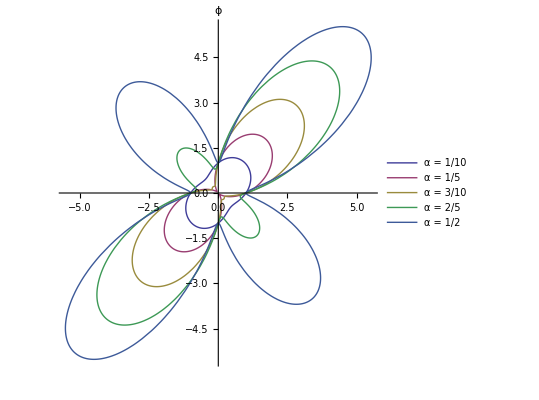

```mathematica
ClearAll[aa, xx, af, pp]
af[a_,p_] = 3 - 2 Cos[ 2 Pi a Cos[p] ] - 2 Cos[ 2 Pi a Sin[p]] + 2 Cos[ 2 Pi a (Cos[p] - Sin[p])] ;
pp = Plot3D[ af[a,p], {a, 0, 1.5}, {p, 0, 2 Pi}, AxesLabel -> {α, ϕ}]

(*aa = {0.5} ;
aa = {0.1, 0.25, 0.5, 0.75, 1} ;*)
aa = Table[i/10, {i, 5}] ;
xx = PolarPlot[af[#, p] &/@ aa // Evaluate, {p, 0, 2 Pi}, AxesLabel -> ϕ, PlotLegends -> Placed[Row[{"α = ", #}]&/@aa, {Right,Bottom}]]

(*peeters`exportForLatex["arrayFactorXYFig4", pp]
peeters`exportForLatex["arrayFactorXYFig5", xx]*)
```

Part (e).  Numerical calculations of the directivity.

```mathematica
ClearAll[Uccube, dir, aa, Umax, Prad]
Uccube[a_, p_, t_] =  Sin[t]^2 (3 - 2 Cos[ 2 Pi a Sin[t]Cos[p] ] - 2 Cos[ 2 Pi a Sin[t]Sin[p]] + 2 Cos[ 2 Pi a Sin[t](Cos[p] - Sin[p])] ) ;
Umax[a_] := 
NMaximize[{Uccube[a, p, t], 0 ≤ p ≤ Pi/2,  0 ≤ t ≤ Pi},{p, t}] ;
Prad[a_] := NIntegrate[Uccube[a, p, t], {p, 0, Pi/2}, {t, 0, Pi}]  ;
dir[a_] := 4 Pi Umax[a][[1]]/Prad[a]  ;
aa = {1/8, 1/4, 1/2} ;

dir[#]&/@ {1/8, 1/4, 1/2}
```

{6.34939,8.11917,10.3841}